```mathematica
h0=0;
α=-3;
β=-2;(*valor del parametro β*)
A0={{Exp[k h0], Exp[-k h0]},{k Exp[k h0], -k Exp[-k h0]}};(*matriz Subscript[A, 0]*)
CA0={{(1-1/4 α β)/(1+1/4 α β),-β/(1+1/4 α β)},{α/(1+1/4 α β),(1-1/4 α β)/(1+1/4 α β)}};(*matriz de condiciones de frontera*)
CD00={{c0},{0}};(*Matriz semilla*)
A00=Inverse[A0] . CA0 . A0 . CD00;(*Matriz Subscript[M, 0]*)
A00[[1,1]]//Simplify(*Elemento correspondiente al término para la ecuación de dispersión*)
A00[[2,1]]//Simplify
```

(c0 (-3-k+2 k^2))/(5 k)

(c0 (3+2 k^2))/(5 k)

```mathematica
κ[k_]:= c0 A00[[1,1]];(*Define la ecuación de dispersión*)
NSolve[κ[k]==0,k,Reals](*Obtiene eigen-valores*)
```

{{k→-1.},{k→1.5}}

```mathematica
kj={1.5};(*Arreglo de k permitidos*)
ϕj[x_,n_]:=Piecewise[{{Exp[kj[[n]]x] ,x<0},{((3+2(kj[[n]])^2)/(5 kj[[n]]))  Exp[-kj[[n]]x] ,x>0}}];
(*Eigen-función*)
Mj[n_]:=√(∫_(-∞)^0 (Abs[ϕj[x,n]])^2 ⅆx+∫_0^∞ (Abs[ϕj[x,n]])^2 ⅆx);(*Const. de normalización*)
Mj[1](*Obtenemos el elemento correspondiente para generar el arreglo de constantes de normalización*)
```

0.816497

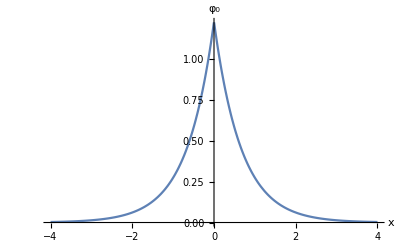

```mathematica
M={0.816496580927726};(*Constantes de normalización de cada eigen-función*)
Plot[1/M[[1]] ϕj[x,1],{x,-4,4},PlotRange->All,AxesLabel->{"x","φ_0"}](*Gráfica de la eigen-función*)
```

```mathematica
(1.5)^2
```

2.25

```mathematica
(3+2(1.5)^2)/(5 (1.5))
```

1.